```mathematica
(* This notebook solves and simulates the TractableBufferStock model *)
```

```mathematica
(* This cell is uninteresting housekeeping and setup stuff; it can be ignored *)
ClearAll["Global`*"];ParamsAreSet=False;
If[$VersionNumber<8,(*then*) Print["These programs require Mathematica version 8 or greater."];Abort[]];
If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
rootDir = SetDirectory["../../.."];
AutoLoadDir=SetDirectory["./Mathematica/CoreCode/Autoload"];Get["./init.m"];
CoreCodeDir=SetDirectory[".."];
rootDir = SetDirectory[".."];
Get[CoreCodeDir<>"/MakeAnalyticalResults.m"];
Get[CoreCodeDir<>"/VarsAndFuncs.m"];
(* Method of creating figures depends on whether being run in batch mode or interactively *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False]; 
FigsDir=SetDirectory[rootDir<>"/Examples/ctDiscrete/Figures/"];
CodeDir=SetDirectory[rootDir<>"/Examples/ctDiscrete"];
```

```mathematica
Get[CoreCodeDir<>"/ParametersBase.m"];
FindStableArm;κEBase = κE;
```

Solving ...

Below 𝓂MinPermitted after 63 backwards Euler iterations.

Last 2 Points:(0.824412 | 0.342591 | 0.330215 | -21.6355 | -0.203069
-0.0283241 | 0.143006 | -2.10391 | -19.4339 | -81.0262)

Solving ...

Above 𝓂MaxPermitted after 119 backwards Euler iterations.

Last 2 Points:(97.6944 | 7.47043 | 0.062828 | -2.17971 | -0.0000302828
102.097 | 7.74672 | 0.0627009 | -2.10364 | -0.0000275432)

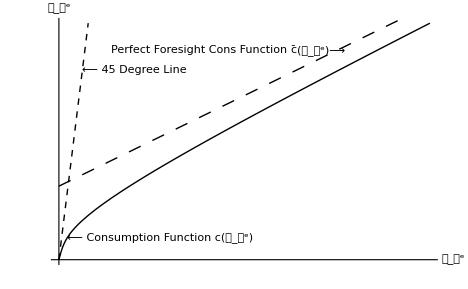

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/TractableBufferStockcFunc.xxx

```mathematica
StableArmStyle={Black,Dashing[{.01}],Thickness[Medium]};
Get[CodeDir<>"/cFunc.m"];
ExportFigsToDir["TractableBufferStockcFunc",FigsDir];
```

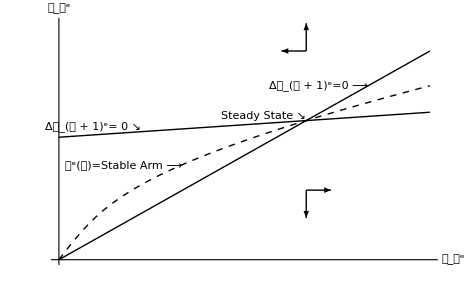

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/TractableBufferStockPhaseDiag.xxx

```mathematica
Get[CodeDir <> "/PhaseDiag.m"];
ExportFigsToDir["TractableBufferStockPhaseDiag",FigsDir];
```

Solving ...

Below 𝓂MinPermitted after 63 backwards Euler iterations.

Last 2 Points:(0.824412 | 0.342591 | 0.330215 | -21.6355 | -0.203069
-0.0283241 | 0.143006 | -2.10391 | -19.4339 | -81.0262)

Solving ...

Above 𝓂MaxPermitted after 119 backwards Euler iterations.

Last 2 Points:(97.6944 | 7.47043 | 0.062828 | -2.17971 | -0.0000302828
102.097 | 7.74672 | 0.0627009 | -2.10364 | -0.0000275432)

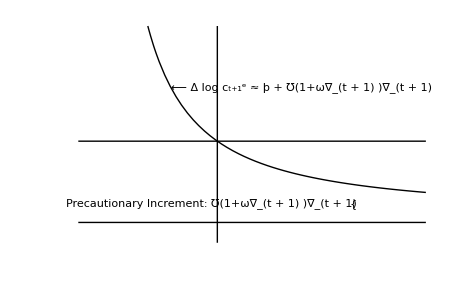

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/TractableBufferStockGrowthA.xxx

```mathematica
Get[CoreCodeDir<>"/ParametersBase.m"];
FindStableArm;κEBase = κE;
HorizAxis=((r)-ϑ)/ρ-0.01;
𝒸GroMaxPlot=Log[𝒞tp1O𝒞t[0.5 𝓂E]];
BufferFigPlot=Show[Plot[Log[𝒞tp1O𝒞t[𝓂]],{𝓂,0.5 𝓂E,2.5 𝓂E}
,Ticks->{{{𝓂E,"(𝓂̌)^e"}},{{𝔤+℧,"γ"},{((r)-ϑ)/ρ,Style["ρ^-1(r-ϑ)≈þ",CharacterEncoding->"WindowsANSI"]}}}
,PlotRange->{{0,2.5 𝓂E},{HorizAxis,𝒸GroMaxPlot}}
]
(*,Graphics[{Dashing[{0.005,0.025}],Thickness[Medium],Black,Line[{{𝓂E,HorizAxis},{𝓂E,𝒸GroMaxPlot}}]}]*)
,Graphics[{Dashing[{}],Thickness[Small],Black,Line[{{𝓂E,HorizAxis},{𝓂E,𝒸GroMaxPlot}}]}]
,Graphics[{Dashing[{}],Thickness[Medium],Line[{{0,𝔤+℧},{2.5 𝓂E,𝔤+℧}}]}]
,Graphics[{Dashing[{}],Thickness[Medium],Line[{{0,((r)-ϑ)/ρ},{2.5 𝓂E,((r)-ϑ)/ρ}}]}
,PlotRange->{{0,2.5 𝓂E},{HorizAxis,𝒸GroMaxPlot}}
]
,AxesOrigin->{((r)-ϑ)/ρ-0.1,HorizAxis}
];
(* The thorn character þ does not appear properly unless encoded with the WindowsANSI encoding, which necessitates the cumbersome apparatus below *)
cLev=Style["c",{Bold,Italic},CharacterEncoding->"WindowsANSI"];
cELevtp1=SubsuperscriptBox[cLev,Style["t+1",CharacterEncoding->"WindowsANSI"],Style["e",CharacterEncoding->"WindowsANSI"]] //DisplayForm;
dLog = Style["Δ log ",CharacterEncoding->"WindowsANSI"];
ArrowPointingLeft = Style[" ⟵ ",CharacterEncoding->"WindowsANSI"];
ArrowPointingRight = Style[" ⟶ ",CharacterEncoding->"WindowsANSI"];
ApproxcELevGro = Style[" ≈ þ + ℧(1+ω∇_(t + 1) )∇_(t + 1) ",CharacterEncoding->"WindowsANSI"];
TractableBufferStockGrowthA=BufferFigBaseline=Show[BufferFigPlot
,Graphics[Text[DisplayForm[RowBox[{ArrowPointingLeft,dLog,cELevtp1,ApproxcELevGro}]],{(𝓂E 2)/3,Log[𝒞tp1O𝒞t[(𝓂E 2)/3]]},{-1,0}]]
,Graphics[Text[" {",{𝓂E 2,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)},{1,0}]]
,Graphics[Text["Precautionary Increment: ℧(1+ω∇_(t + 1) )∇_(t + 1)    ",{𝓂E 2,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)},{1,0}]]
,Axes->{Automatic,Automatic}
,AxesLabel->{"𝓂_𝓉^e","Growth"}
,AxesOrigin->{((r)-ϑ)/ρ-0.1,HorizAxis}
,PlotRange->{{((r)-ϑ)/ρ-0.1,2.5 𝓂E},{HorizAxis,𝒸GroMaxPlot}}];
ExportFigsToDir["TractableBufferStockGrowthA",FigsDir];
TractableBufferStockGrowthA;
```

Solving ...

Below 𝓂MinPermitted after 122 backwards Euler iterations.

Last 2 Points:(1.27142 | 0.536822 | 0.280024 | -15.2619 | -0.162798
0.522204 | 0.267269 | 0.454929 | -20.1988 | -0.270155)

Solving ...

Above 𝓂MaxPermitted after 235 backwards Euler iterations.

Last 2 Points:(97.994 | 8.75666 | 0.0785622 | -1.45757 | -6.33253×10^-6
100.02 | 8.91581 | 0.0785498 | -1.43162 | -5.96016×10^-6)

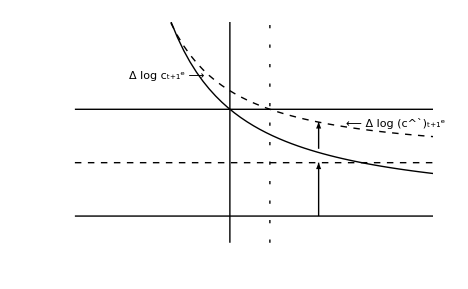

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/TractableBufferStockGrowthB.xxx

```mathematica
r = rBase+.04;
FindStableArm;
cEModLevtp1=SubsuperscriptBox[OverscriptBox[Style["c",{Bold,Italic},CharacterEncoding->"WindowsANSI"],"`"],Style["t+1",Plain],Style["e",Plain]];
BufferFigNew = Plot[
Log[𝒞tp1O𝒞t[𝓂]],{𝓂,0.5 𝓂EBase,2.5 𝓂EBase}
,PlotStyle->{Dashing[{.01}],Thickness[Medium],Black}];
TractableBufferStockGrowthB=Show[BufferFigPlot
,BufferFigNew
,Graphics[Text[DisplayForm[RowBox[{ArrowPointingLeft,dLog,cEModLevtp1}]],{(𝓂EBase 14)/8,Log[𝒞tp1O𝒞t[(𝓂EBase 13)/8]]},{-1,0}]]
,Graphics[Text[DisplayForm[RowBox[{dLog, cELevtp1, ArrowPointingRight,"   "}]],{(𝓂EBase 5)/6,Log[𝒞tp1O𝒞t[(𝓂EBase 5)/6]]},{1,1}]]
,Graphics[{Dashing[{0.005,0.025}],Thickness[Medium],Line[{{𝓂E,HorizAxis},{𝓂E,Log[𝒞tp1O𝒞t[1.5]]}}]}]
,Graphics[{Dashing[{0.01}],Thickness[Medium],Line[{{0,((r)-ϑ)/ρ},{2.5 𝓂EBase,((r)-ϑ)/ρ}}]}]
,PhaseArrow[{𝓂E 1.25,(rBase-ϑ)/ρ},{𝓂E 1.25,((r)-ϑ)/ρ}]
,PhaseArrow[{𝓂E 1.25,Log[𝒞tp1O𝒞t[𝓂E 1.25]]-(((r)-rBase) 2)/(ρ 4)},{𝓂E 1.25,Log[𝒞tp1O𝒞t[𝓂E 1.25]]}]
,Axes->{Automatic,Automatic}
,AxesLabel->{"𝓂_𝓉","Growth"}
,AxesOrigin->{Automatic,HorizAxis}
,Ticks->{{{𝓂EBase,"m̌"},{𝓂E,"(𝓂̌)^`"}},{{𝔤+℧,"γ"},{(rBase-ϑ)/ρ,
Style["ρ^-1(𝓇-ϑ)≈þ",CharacterEncoding->"WindowsANSI"]},{((r)-ϑ)/ρ,Style["ρ^-1(𝓇^`-ϑ)≈þ^`",CharacterEncoding->"WindowsANSI"]}}}
,PlotRange->{{0,1.8 𝓂E},{HorizAxis,Log[𝒞tp1O𝒞t[0.5𝓂E]]}}];
ExportFigsToDir["TractableBufferStockGrowthB",FigsDir];
TractableBufferStockGrowthB;
```

```mathematica
r = rBase;
ϑ=ϑBase-0.02;
FindStableArm;
𝓂Max0=𝓂Max;
cFuncPlotNew=Plot[cE[𝓂],{𝓂,0,𝓂Max0},PlotStyle->{Black,Thickness[Medium]}];
cFuncPlotNewPoints=Map[{{#,𝒸[#]}}&,Table[𝓂,{𝓂,0,𝓂Max0,0.01}]];
Stable𝓂LocusPlot=Plot[{𝓂EDelEqZero[𝓂]},{𝓂,0,𝓂Max0},PlotStyle->{Dashing[{.01}],Thickness[Medium],Black}];
Stable𝓂LocusPoints=Map[{{#,𝓂EDelEqZero[#]}}&,Table[𝓂,{𝓂,0,𝓂Max0,0.1}]];
```

Solving ...

Below 𝓂MinPermitted after 92 backwards Euler iterations.

Last 2 Points:(0.994206 | 0.358123 | 0.266725 | -25.8708 | -0.158377
-0.00128 | 0.00437307 | -3.41433 | 43.1759 | -4.98888)

Solving ...

Above 𝓂MaxPermitted after 160 backwards Euler iterations.

Last 2 Points:(97.66 | 6.46635 | 0.0537865 | -2.94138 | -0.0000266077
100.96 | 6.6437 | 0.0537019 | -2.86457 | -0.000024729)

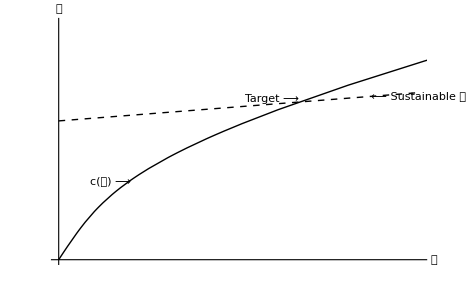

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/TractableBufferStockTarget.xxx

-Graphics-

```mathematica
SetOptions[ListPlot,PlotStyle->Black];SimGeneratePath[𝓂EBase,200];
𝓂𝒸PathPlot = ListPlot[𝓂𝒸Path,PlotStyle->{Black,PointSize[0.008]}];
{𝓂MinNew,𝓂MaxNew}={0,2 𝓂EBase};
{𝒸MinNew,𝒸MaxPlotNew}={0,1.5 𝒸EBase};
TractableBufferStockTarget = Show[cFuncPlotBase,Stable𝓂LocusPlot
,Graphics[Text["Target ⟶",{𝓂EBase,1.02𝒸EBase},{1,0}]]
,Graphics[Text["     ⟵ Sustainable 𝒸",{1.3 𝓂EBase,𝓂EDelEqZero[1.3 𝓂EBase]},{-1,0}]]
,Graphics[Text["c(𝓂) ⟶   ",{0.3𝓂EBase,0.5𝒸EBase},{1,0}]]
,Ticks->None
,PlotRange->{{𝓂MinNew,𝓂Max},{𝒸MinNew,𝒸MaxPlotNew}}
,AxesLabel->{"𝓂","𝒸"}];
OldAndNewcFuncsPlot = Show[Stable𝓂LocusPlot,cFuncPlotBase,cFuncPlotNew
,PlotRange->{{0,𝓂Max},{0,Automatic}}
,AxesOrigin->{0.,0.}
];
ExportFigsToDir["TractableBufferStockTarget",FigsDir];Show[TractableBufferStockTarget]
```

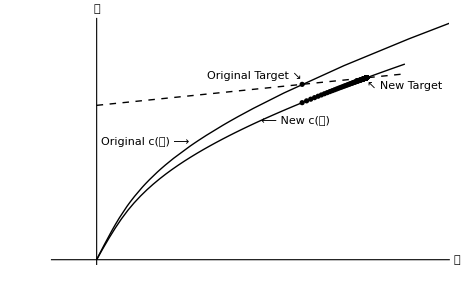

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/PhaseDiagramDecreaseThetaPlot.xxx

-Graphics-

```mathematica
PhaseDiagramDecreaseThetaPlot = Show[OldAndNewcFuncsPlot,𝓂𝒸PathPlot
,Graphics[Text["Original Target ↘ ",{𝓂EBase,1.02𝒸EBase},{1,-1}]]
,Graphics[Text["↖ New Target ",{𝓂E,0.98𝒸E},{-1,1}]]
,Graphics[Text["Original c(𝓂) ⟶",{0.45𝓂EBase,0.67𝒸EBase},{1,0}]]
,Graphics[Text[" ⟵ New c(𝓂)",{0.8𝓂EBase,cE[0.8𝓂EBase]},{-1,0}]]
,Ticks->None
,AxesLabel->{"𝓂","𝒸"}
,PlotRange->{{𝓂MinNew-1,𝓂E+2},{𝒸MinNew,1.3𝒸E}}
,AxesOrigin->{0.,0.}
];
ExportFigsToDir["PhaseDiagramDecreaseThetaPlot",FigsDir];
Show[PhaseDiagramDecreaseThetaPlot]
```

```mathematica
HowMany=75;
𝓂Path=Take[Transpose[𝓂𝒸Path][[1]],HowMany];
𝒸Path=Take[Transpose[𝓂𝒸Path][[2]],HowMany];
MPCPath=Map[cE'[#]&,Rest[𝓂Path]];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
timePath=Table[i,{i,Length[𝒸Path]}];
𝒸PathPlot = ListPlot[Transpose[{timePath,𝒸Path}],PlotRange->All];
𝓂PathPlot = ListPlot[Transpose[{timePath,𝓂Path}],PlotRange->All];
MPCPathPlot = ListPlot[Transpose[{timePath,MPCPath}],PlotRange->All];
```

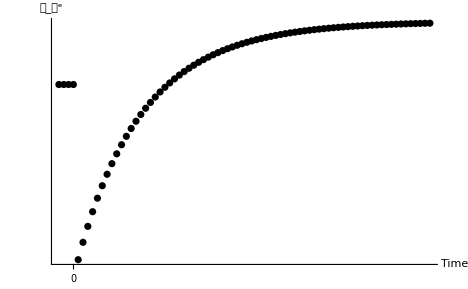

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/cPathAfterThetaDrop.xxx

-Graphics-

```mathematica
cPathAfterThetaDrop=Show[𝒸PathPlot
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","𝒸_𝓉^e"}
,AxesOrigin->{-3,0}
,PlotRange->{{-3,Automatic},{0,Automatic}}
];
ExportFigsToDir["cPathAfterThetaDrop",FigsDir];
Print[Show[cPathAfterThetaDrop]];
```

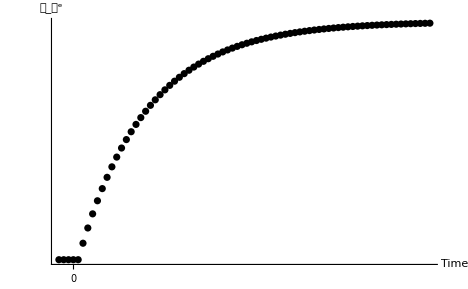

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/mPathAfterThetaDrop.xxx

-Graphics-

```mathematica
mPathAfterThetaDrop=Show[𝓂PathPlot
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","𝓂_𝓉^e"}
,PlotRange->{{-3,HowMany},{0,Automatic}}
,AxesOrigin->{-3,0}
,PlotRange->{{-3,Automatic},{0,Automatic}}
];
ExportFigsToDir["mPathAfterThetaDrop",FigsDir];
Print[Show[mPathAfterThetaDrop]];
```

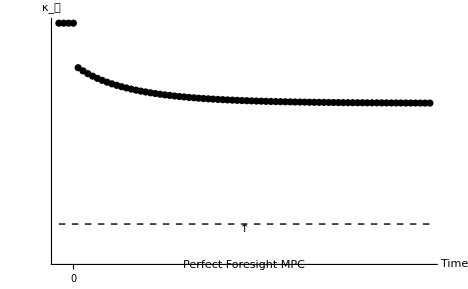

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/MPCPathAfterThetaDrop.xxx

```mathematica
MPCPathAfterThetaDrop=Show[MPCPathPlot
,Graphics[{Dashing[{0.01}],Line[{{timePath[[1]],κ},{timePath[[-1]],κ}}]}]
,Graphics[Text["↑",{(timePath[[1]]+timePath[[-1]])/2,κ},{0,1}]]
,Graphics[Text["Perfect Foresight MPC",{(timePath[[1]]+timePath[[-1]])/2,κ(4/5)},{0,1}]]
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","κ_𝓉"}
,PlotRange->All
,AxesOrigin->{-3,0.}];
ExportFigsToDir["MPCPathAfterThetaDrop",FigsDir];
```

```mathematica
Get[CoreCodeDir<>"/ParametersBase.m"];
FindStableArm;κEBase = κE;𝓂EBase=𝓂E;𝒸EBase=𝒸E;
```

Solving ...

Below 𝓂MinPermitted after 63 backwards Euler iterations.

Last 2 Points:(0.824412 | 0.342591 | 0.330215 | -21.6355 | -0.203069
-0.0283241 | 0.143006 | -2.10391 | -19.4339 | -81.0262)

Solving ...

Above 𝓂MaxPermitted after 119 backwards Euler iterations.

Last 2 Points:(97.6944 | 7.47043 | 0.062828 | -2.17971 | -0.0000302828
102.097 | 7.74672 | 0.0627009 | -2.10364 | -0.0000275432)

```mathematica
{mMaxPlot,mMaxPlot}={1.5,5} 𝓂E;
𝒸LowerPlot=Plot[cE[𝓂],{𝓂,0,mMaxPlot},PlotStyle->Dashing[{.01}]];
cEPFPlot = Plot[cEPF[𝓂],{𝓂,0,mMaxPlot},PlotStyle->Dashing[{.02}]];
Degree45 = Plot[𝓂,{𝓂,0,cE[mMaxPlot]},PlotStyle->Dashing[{.01}]];
cFuncPlotBase=cFuncPlot=Plot[cE[𝓂],{𝓂,0,mMaxPlot},PlotStyle->Black];
BufferFigOrig=Show[Plot[Log[𝒞tp1O𝒞t[𝓂]],{𝓂,0.5 𝓂E,2.1 𝓂E}
,Ticks->{{{𝓂E,"(𝓂̌)^e"}},{{𝔤+℧,"γ"},{((r)-ϑ)/ρ,Style["ρ^-1(r-ϑ)≈þ",CharacterEncoding->"WindowsANSI"]}}}
,PlotRange->{{0,2.1 𝓂E},{HorizAxis,𝒸GroMaxPlot}}
]
(*,Graphics[{Dashing[{0.005,0.025}],Thickness[Medium],Black,Line[{{𝓂E,HorizAxis},{𝓂E,𝒸GroMaxPlot}}]}]*)
,Graphics[{Dashing[{}],Thickness[Small],Black,Line[{{𝓂E,HorizAxis},{𝓂E,𝒸GroMaxPlot}}]}]
,Graphics[{Dashing[{}],Thickness[Medium],Line[{{0,𝔤+℧},{2.1 𝓂E,𝔤+℧}}]}]
,Graphics[{Dashing[{}],Thickness[Medium],Line[{{0,((r)-ϑ)/ρ},{2.1 𝓂E,((r)-ϑ)/ρ}}]}
,PlotRange->{{0,2.1 𝓂E},{HorizAxis,𝒸GroMaxPlot}}
]
,AxesOrigin->{((r)-ϑ)/ρ-0.1,HorizAxis}
];
```

```mathematica
Stable𝓂LocusOrigPlot=Plot[{𝓂EDelEqZero[𝓂]},{𝓂,0,mMaxPlot},PlotStyle->{Black,Dashing[{.01}],Thickness[Medium]}];

℧=3 ℧Base;
FindStableArm;
cFuncPlotNew=Plot[cE[𝓂],{𝓂,0,mMaxPlot},PlotStyle->RGBColor[0,0,0]];
cFuncPlotNewPoints=Map[{{#,𝒸[#]}}&,Table[𝓂,{𝓂,0,mMaxPlot,0.01}]];
Stable𝓂LocusPlot=Plot[{𝓂EDelEqZero[𝓂]},{𝓂,0,mMaxPlot},PlotStyle->{Black,Dashing[{.01}],Thickness[Medium]}];
Stable𝓂LocusPoints=Map[{{#,𝓂EDelEqZero[#]}}&,Table[𝓂,{𝓂,0,mMaxPlot,0.1}]];
```

Solving ...

Below 𝓂MinPermitted after 76 backwards Euler iterations.

Last 2 Points:(0.798029 | 0.241007 | 0.246965 | -32.4168 | -0.126938
-0.102219 | 0.096856 | -0.671293 | -20.7631 | -6.2002)

Solving ...

Above 𝓂MaxPermitted after 121 backwards Euler iterations.

Last 2 Points:(96.5331 | 7.15217 | 0.0631531 | -2.26869 | -0.0000310545
101.637 | 7.47412 | 0.0630026 | -2.17321 | -0.0000279868)

```mathematica
SimGeneratePath[𝓂EBase,100];
𝓂𝒸PathPlot = ListPlot[𝓂𝒸Path,PlotStyle->{Black,PointSize[0.007]}];
{𝓂MinNew,𝓂Max}={0,5};
{𝒸MinNew,𝒸MaxPlotNew}={0,1.5};
TractableBufferStockTarget = Show[cFuncPlotBase,Stable𝓂LocusPlot,Stable𝓂LocusOrigPlot
,Graphics[Text["Target ⟶",{𝓂EBase,1.02𝒸EBase},{1,0}]]
,Graphics[Text[" ⟵ Sustainable 𝒸",{𝓂E,0.98𝒸E},{-1,0}]]
,Graphics[Text["c(𝓂) ⟶",{0.7𝓂EBase,0.85𝒸EBase},{1,0}]]
,Ticks->None
,PlotRange->{{𝓂MinNew,𝓂Max},{𝒸MinNew,𝒸MaxPlotNew}}
,AxesLabel->{"𝓂","𝒸"}];
OldAndNewcFuncsPlot = Show[Stable𝓂LocusPlot,cFuncPlotBase,cFuncPlotNew
,PlotRange->{{0,mMaxPlot},{0,Automatic}}
,AxesOrigin->{0.,0.}
];
```

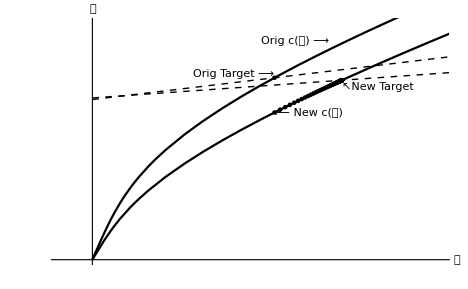

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/PhaseDiagramIncreaseMhoPlot.xxx

```mathematica
PhaseDiagramIncreaseMhoPlot = Show[OldAndNewcFuncsPlot,𝓂𝒸PathPlot,Stable𝓂LocusOrigPlot
,Graphics[Text["Orig Target ⟶",{𝓂EBase,1.02𝒸EBase},{1,0}]]
,Graphics[Text["↖New Target",{𝓂E,0.96𝒸E},{-1,0}]]
,Graphics[Text["Orig c(𝓂) ⟶",{1.3𝓂EBase,1.2𝒸EBase},{1,0}]]
,Graphics[Text[" ⟵ New c(𝓂)",{𝓂EBase,cE[𝓂EBase]},{-1,0}]]
,Ticks->None
,AxesLabel->{"𝓂","𝒸"}
,PlotRange->{{𝓂MinNew-1,𝓂E+3},{𝒸MinNew,1.3𝒸EBase}}
,AxesOrigin->{0.,0.}
];
ExportFigsToDir["PhaseDiagramIncreaseMhoPlot",FigsDir];
```

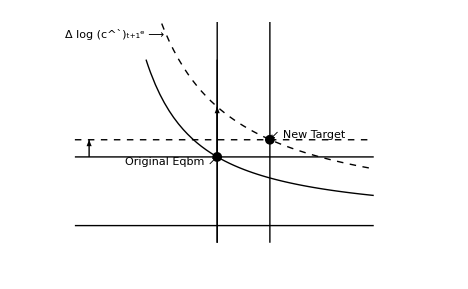

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/cGroIncreaseMhoPlot.xxx

-Graphics-

```mathematica
cEModLevtp1=SubsuperscriptBox[OverscriptBox[Style["c",{Bold,Italic},CharacterEncoding->"WindowsANSI"],"`"],Style["t+1",Plain],Style["e",Plain]];
BufferFigNew = Plot[
Log[𝒞tp1O𝒞t[𝓂]],{𝓂,0.5 𝓂EBase,2.1 𝓂EBase}
,PlotStyle->{Dashing[{.01}],Thickness[Medium],Black}];
cGroIncreaseMhoPlot=Show[BufferFigOrig
,BufferFigNew
(*,Graphics[Text[DisplayForm[RowBox[{ArrowPointingLeft,dLog,cEModLevtp1}]],{(𝓂EBase 14)/8,Log[𝒞tp1O𝒞t[(𝓂EBase 13)/8]]},{-1,0}]]*)
,Graphics[Text[DisplayForm[RowBox[{dLog, cEModLevtp1,ArrowPointingRight}]],{(𝓂EBase 7.5)/12,Log[𝒞tp1O𝒞t[(𝓂EBase 7.5)/12]]},{1,1}]]
,Graphics[{Dashing[{}],Thickness[Small],Line[{{𝓂E,HorizAxis},{𝓂E,Log[𝒞tp1O𝒞t[1.5]]}}]}]
(*,Graphics[{Dashing[{0.01}],Thickness[Medium],Line[{{0,((r)-ϑ)/ρ},{2.0 𝓂EBase,((r)-ϑ)/ρ}}]}]*)
,Graphics[{Dashing[{}],Thickness[Small],Black,Line[{{𝓂EBase,HorizAxis},{𝓂EBase,Log[𝒞tp1O𝒞t[1.5]]}}]}]
,Graphics[{Dashing[{0.01}],Thickness[Medium],Line[{{0,𝔤+℧},{2.1 𝓂EBase,𝔤+℧}}]}]
(*,Graphics[Text[" {",{𝓂E 1.65,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)-0.003},{1,0}]]*)
(*,Graphics[Text["℧(1+ω∇_(t + 1) )∇_(t + 1)    ",{𝓂E 1.65,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)-0.003},{1,0}]]*)
(*,Graphics[Text[" }",{𝓂E 1.65,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)+0.001},{-1,0}]]*)
(*,Graphics[Text["℧^`(1+ω(∇^`)_(t + 1))(∇^`)_(t + 1)",{𝓂E 1.85,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)+0.001},{-1,0}]]*)
,Graphics[Text["Original Eqbm ↗",{𝓂EBase,𝔤+℧Base},{1,1}]]
,Graphics[Text[" ↙ New Target",{𝓂E,𝔤+℧},{-1,-1}]]
,Graphics[{PointSize[0.015],Point[{𝓂EBase,𝔤+℧Base}]}]
,Graphics[{PointSize[0.015],Point[{𝓂E,𝔤+℧}]}]
,PhaseArrow[{0.1 𝓂EBase,𝔤+℧Base},{0.1 𝓂EBase,𝔤+℧}]
,PhaseArrow[{𝓂EBase,𝔤+℧Base},{𝓂EBase,Log[𝒞tp1O𝒞t[𝓂EBase]]}]
,Axes->{Automatic,Automatic}
,AxesLabel->{"𝓂_𝓉","Growth"}
,AxesOrigin->{Automatic,HorizAxis}
,Ticks->{{{𝓂EBase,"m̌"}
,{𝓂E,"(𝓂̌)^`"}}
,{{𝔤+℧Base,"γ"}
,{𝔤+℧,"γ^`"}
,{(rBase-ϑ)/ρ,Style["ρ^-1(𝓇-ϑ)≈þ",CharacterEncoding->"WindowsANSI"]}
(*,{((r)-ϑ)/ρ,Style["ρ^-1(𝓇^`-ϑ)≈þ^`",CharacterEncoding->"WindowsANSI"]}*)
}}
(*,PlotRange->{{0,2.6 𝓂E},{HorizAxis,Log[𝒞tp1O𝒞t[0.5𝓂E]]}}*)
,PlotRange->{{0,1.8 𝓂E},{HorizAxis,Log[𝒞tp1O𝒞t[0.45𝓂E]]}}
];
ExportFigsToDir["cGroIncreaseMhoPlot",FigsDir];
cGroIncreaseMhoPlot
```

```mathematica
HowMany=75;
𝓂Path=Take[Transpose[𝓂𝒸Path][[1]],HowMany];
𝒸Path=Take[Transpose[𝓂𝒸Path][[2]],HowMany];
MPCPath=Map[cE'[#]&,Rest[𝓂Path]];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
timePath=Table[i,{i,Length[𝒸Path]}];
𝒸PathPlot = ListPlot[Transpose[{timePath,𝒸Path}],PlotRange->All];
𝓂PathPlot = ListPlot[Transpose[{timePath,𝓂Path}],PlotRange->All];
MPCPathPlot = ListPlot[Transpose[{timePath,MPCPath}],PlotRange->All];
```

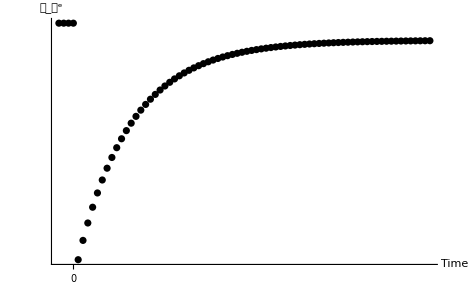

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/cPathAfterMhoRise.xxx

```mathematica
cPathAfterMhoRise=Show[𝒸PathPlot
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","𝒸_𝓉^e"}
,AxesOrigin->{-3,0}
,PlotRange->{{-3,Automatic},{0,Automatic}}
];
ExportFigsToDir["cPathAfterMhoRise",FigsDir];
```

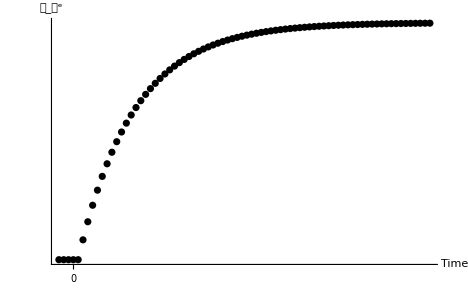

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/mPathAfterMhoRise.xxx

```mathematica
mPathAfterMhoRise=Show[𝓂PathPlot
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","𝓂_𝓉^e"}
,PlotRange->{{-3,HowMany},{0,Automatic}}
,AxesOrigin->{-3,0}
,PlotRange->{{-3,Automatic},{0,Automatic}}
];
ExportFigsToDir["mPathAfterMhoRise",FigsDir];
```

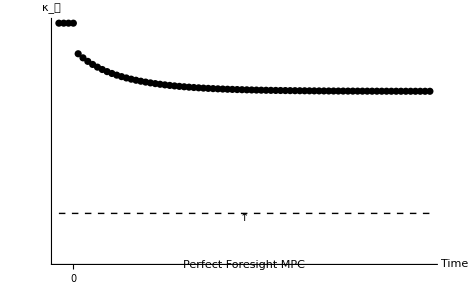

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/MPCPathAfterMhoRise.xxx

```mathematica
MPCPathAfterMhoRise=Show[MPCPathPlot
,Graphics[{Dashing[{0.01}],Line[{{timePath[[1]],κ},{timePath[[-1]],κ}}]}]
,Graphics[Text["↑",{(timePath[[1]]+timePath[[-1]])/2,κ},{0,1}]]
,Graphics[Text["Perfect Foresight MPC",{(timePath[[1]]+timePath[[-1]])/2,κ(4/5)},{0,1}]]
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","κ_𝓉"}
,PlotRange->All
,AxesOrigin->{-3,0.}];
ExportFigsToDir["MPCPathAfterMhoRise",FigsDir];
```

```mathematica
(* Now decrease expected income growth *)
Get[CoreCodeDir<>"/ParametersBase.m"];
FindStableArm;κEBase = κE;𝓂EBase=𝓂E;𝒸EBase=𝒸E;
```

Solving ...

Below 𝓂MinPermitted after 63 backwards Euler iterations.

Last 2 Points:(0.824412 | 0.342591 | 0.330215 | -21.6355 | -0.203069
-0.0283241 | 0.143006 | -2.10391 | -19.4339 | -81.0262)

Solving ...

Above 𝓂MaxPermitted after 119 backwards Euler iterations.

Last 2 Points:(97.6944 | 7.47043 | 0.062828 | -2.17971 | -0.0000302828
102.097 | 7.74672 | 0.0627009 | -2.10364 | -0.0000275432)

```mathematica
{mMaxPlot,mMaxPlot}={1.5,5} 𝓂E;
𝒸LowerPlot=Plot[cE[𝓂],{𝓂,0,mMaxPlot},PlotStyle->Dashing[{.01}]];
cEPFPlot = Plot[cEPF[𝓂],{𝓂,0,mMaxPlot},PlotStyle->Dashing[{.02}]];
Degree45 = Plot[𝓂,{𝓂,0,cE[mMaxPlot]},PlotStyle->Dashing[{.01}]];
cFuncPlotBase=cFuncPlot=Plot[cE[𝓂],{𝓂,0,mMaxPlot},PlotStyle->Black];
BufferFigOrig=Show[Plot[Log[𝒞tp1O𝒞t[𝓂]],{𝓂,0.5 𝓂E,2.1 𝓂E}
,Ticks->{{{𝓂E,"(𝓂̌)^e"}},{{𝔤+℧,"γ"},{((r)-ϑ)/ρ,Style["ρ^-1(r-ϑ)≈þ",CharacterEncoding->"WindowsANSI"]}}}
,PlotRange->{{0,2.1 𝓂E},{HorizAxis,𝒸GroMaxPlot}}
]
(*,Graphics[{Dashing[{0.005,0.025}],Thickness[Medium],Black,Line[{{𝓂E,HorizAxis},{𝓂E,𝒸GroMaxPlot}}]}]*)
,Graphics[{Dashing[{}],Thickness[Small],Black,Line[{{𝓂E,HorizAxis},{𝓂E,𝒸GroMaxPlot}}]}]
,Graphics[{Dashing[{}],Thickness[Medium],Line[{{0,𝔤+℧},{2.1 𝓂E,𝔤+℧}}]}]
,Graphics[{Dashing[{}],Thickness[Medium],Line[{{0,((r)-ϑ)/ρ},{2.1 𝓂E,((r)-ϑ)/ρ}}]}
,PlotRange->{{0,2.1 𝓂E},{HorizAxis,𝒸GroMaxPlot}}
]
,AxesOrigin->{((r)-ϑ)/ρ-0.1,HorizAxis}
];
```

```mathematica
Stable𝓂LocusOrigPlot=Plot[{𝓂EDelEqZero[𝓂]},{𝓂,0,mMaxPlot},PlotStyle->{Black,Dashing[{.01}],Thickness[Medium]}];

𝔤   =-0.02;

FindStableArm;
cFuncPlotNew=Plot[cE[𝓂],{𝓂,0,mMaxPlot},PlotStyle->RGBColor[0,0,0]];
cFuncPlotNewPoints=Map[{{#,𝒸[#]}}&,Table[𝓂,{𝓂,0,mMaxPlot,0.01}]];
Stable𝓂LocusPlot=Plot[{𝓂EDelEqZero[𝓂]},{𝓂,0,mMaxPlot},PlotStyle->{Black,Dashing[{.01}],Thickness[Medium]}];
Stable𝓂LocusPoints=Map[{{#,𝓂EDelEqZero[#]}}&,Table[𝓂,{𝓂,0,mMaxPlot,0.1}]];
```

Solving ...

Below 𝓂MinPermitted after 148 backwards Euler iterations.

Last 2 Points:(1.49144 | 0.51391 | 0.216579 | -20.2176 | -0.104484
0.801589 | 0.331653 | 0.325197 | -24.1463 | -0.217942)

Solving ...

Above 𝓂MaxPermitted after 257 backwards Euler iterations.

Last 2 Points:(98.5042 | 7.08815 | 0.0611063 | -2.3239 | -0.0000109261
100.444 | 7.20665 | 0.0610857 | -2.28593 | -0.0000103572)

```mathematica
SimGeneratePath[𝓂EBase,100];
𝓂𝒸PathPlot = ListPlot[𝓂𝒸Path,PlotStyle->{Black,PointSize[0.007]}];
{𝓂MinNew,𝓂Max}={0,5};
{𝒸MinNew,𝒸MaxPlotNew}={0,1.5};
TractableBufferStockTarget = Show[cFuncPlotBase,Stable𝓂LocusPlot,Stable𝓂LocusOrigPlot
,Graphics[Text["Target ⟶",{𝓂EBase,1.02𝒸EBase},{1,0}]]
,Graphics[Text[" ⟵ Sustainable 𝒸",{𝓂E,0.98𝒸E},{-1,0}]]
,Graphics[Text["c(𝓂) ⟶",{0.7𝓂EBase,0.85𝒸EBase},{1,0}]]
,Ticks->None
,PlotRange->{{𝓂MinNew,𝓂Max},{𝒸MinNew,𝒸MaxPlotNew}}
,AxesLabel->{"𝓂","𝒸"}];
OldAndNewcFuncsPlot = Show[Stable𝓂LocusPlot,cFuncPlotBase,cFuncPlotNew
,PlotRange->{{0,mMaxPlot},{0,Automatic}}
,AxesOrigin->{0.,0.}
];
```

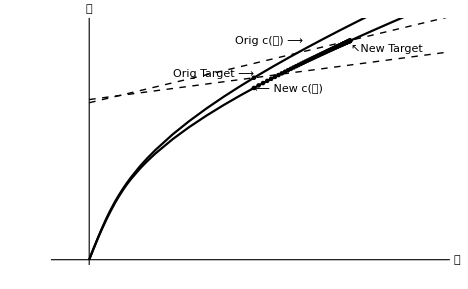

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/PhaseDiagramAfterGFallPlot.xxx

```mathematica
PhaseDiagramAfterGFallPlot = Show[OldAndNewcFuncsPlot,𝓂𝒸PathPlot,Stable𝓂LocusOrigPlot
,Graphics[Text["Orig Target ⟶",{𝓂EBase,1.02𝒸EBase},{1,0}]]
,Graphics[Text["↖New Target",{𝓂E,0.96𝒸E},{-1,0}]]
,Graphics[Text["Orig c(𝓂) ⟶",{1.3𝓂EBase,1.2𝒸EBase},{1,0}]]
,Graphics[Text[" ⟵ New c(𝓂)",{𝓂EBase,cE[𝓂EBase]},{-1,0}]]
,Ticks->None
,AxesLabel->{"𝓂","𝒸"}
,PlotRange->{{𝓂MinNew-1,𝓂E+3},{𝒸MinNew,1.3𝒸EBase}}
,AxesOrigin->{0.,0.}
];
ExportFigsToDir["PhaseDiagramAfterGFallPlot",FigsDir];
```

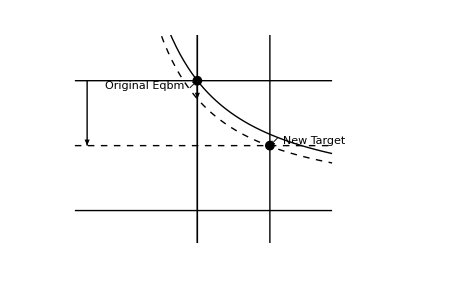

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/cGroAfterGFallPlot.xxx

```mathematica
cEModLevtp1=SubsuperscriptBox[OverscriptBox[Style["c",{Bold,Italic},CharacterEncoding->"WindowsANSI"],"`"],Style["t+1",Plain],Style["e",Plain]];
BufferFigNew = Plot[
Log[𝒞tp1O𝒞t[𝓂]],{𝓂,0.5 𝓂EBase,2.1 𝓂EBase}
,PlotStyle->{Dashing[{.01}],Thickness[Medium],Black}];
cGroAfterGFallPlot=Show[BufferFigOrig
,BufferFigNew
(*,Graphics[Text[DisplayForm[RowBox[{ArrowPointingLeft,dLog,cEModLevtp1}]],{(𝓂EBase 14)/8,Log[𝒞tp1O𝒞t[(𝓂EBase 13)/8]]},{-1,0}]]*)
,Graphics[Text[DisplayForm[RowBox[{dLog, cEModLevtp1,ArrowPointingRight}]],{(𝓂EBase 7.5)/12,Log[𝒞tp1O𝒞t[(𝓂EBase 7.5)/12]]},{1,1}]]
,Graphics[{Dashing[{}],Thickness[Small],Line[{{𝓂E,HorizAxis},{𝓂E,Log[𝒞tp1O𝒞t[1.5]]}}]}]
(*,Graphics[{Dashing[{0.01}],Thickness[Medium],Line[{{0,((r)-ϑ)/ρ},{2.0 𝓂EBase,((r)-ϑ)/ρ}}]}]*)
,Graphics[{Dashing[{}],Thickness[Small],Black,Line[{{𝓂EBase,HorizAxis},{𝓂EBase,Log[𝒞tp1O𝒞t[1.5]]}}]}]
,Graphics[{Dashing[{0.01}],Thickness[Medium],Line[{{0,𝔤+℧},{2.1 𝓂EBase,𝔤+℧}}]}]
(*,Graphics[Text[" {",{𝓂E 1.65,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)-0.003},{1,0}]]*)
(*,Graphics[Text["℧(1+ω∇_(t + 1) )∇_(t + 1)    ",{𝓂E 1.65,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)-0.003},{1,0}]]*)
(*,Graphics[Text[" }",{𝓂E 1.65,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)+0.001},{-1,0}]]*)
(*,Graphics[Text["℧^`(1+ω(∇^`)_(t + 1))(∇^`)_(t + 1)",{𝓂E 1.85,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)+0.001},{-1,0}]]*)
,Graphics[Text["Original Eqbm ↗",{𝓂EBase,𝔤Base+℧},{1,1}]]
,Graphics[Text[" ↙ New Target",{𝓂E,𝔤+℧},{-1,-1}]]
,Graphics[{PointSize[0.015],Point[{𝓂EBase,𝔤Base+℧}]}]
,Graphics[{PointSize[0.015],Point[{𝓂E,𝔤+℧}]}]
,PhaseArrow[{0.1 𝓂EBase,𝔤Base+℧},{0.1 𝓂EBase,𝔤+℧}]
,PhaseArrow[{𝓂EBase,𝔤Base+℧},{𝓂EBase,Log[𝒞tp1O𝒞t[𝓂EBase]]}]
,Axes->{Automatic,Automatic}
,AxesLabel->{"𝓂_𝓉","Growth"}
,AxesOrigin->{Automatic,HorizAxis}
,Ticks->{{{𝓂EBase,"m̌"}
,{𝓂E,"(𝓂̌)^`"}}
,{{𝔤Base+℧,"γ"}
,{𝔤+℧,"γ^`"}
,{(rBase-ϑ)/ρ,Style["ρ^-1(𝓇-ϑ)≈þ",CharacterEncoding->"WindowsANSI"]}
(*,{((r)-ϑ)/ρ,Style["ρ^-1(𝓇^`-ϑ)≈þ^`",CharacterEncoding->"WindowsANSI"]}*)
}}
(*,PlotRange->{{0,2.6 𝓂E},{HorizAxis,Log[𝒞tp1O𝒞t[0.5𝓂E]]}}*)
,PlotRange->{{0,1.8 𝓂E},{HorizAxis,Log[𝒞tp1O𝒞t[0.45𝓂E]]}}
];
ExportFigsToDir["cGroAfterGFallPlot",FigsDir];
```

```mathematica
HowMany=75;
𝓂Path=Take[Transpose[𝓂𝒸Path][[1]],HowMany];
𝒸Path=Take[Transpose[𝓂𝒸Path][[2]],HowMany];
MPCPath=Map[cE'[#]&,Rest[𝓂Path]];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
timePath=Table[i,{i,Length[𝒸Path]}];
𝒸PathPlot = ListPlot[Transpose[{timePath,𝒸Path}],PlotRange->All];
𝓂PathPlot = ListPlot[Transpose[{timePath,𝓂Path}],PlotRange->All];
MPCPathPlot = ListPlot[Transpose[{timePath,MPCPath}],PlotRange->All];
```

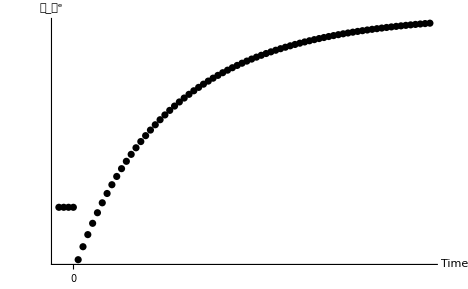

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/cPathAfterGFall.xxx

```mathematica
cPathAfterGFall=Show[𝒸PathPlot
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","𝒸_𝓉^e"}
,AxesOrigin->{-3,0}
,PlotRange->{{-3,Automatic},{0,Automatic}}
];
ExportFigsToDir["cPathAfterGFall",FigsDir];
```

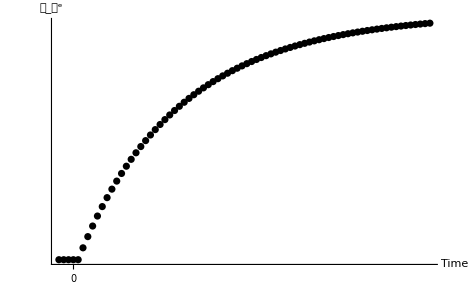

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/mPathAfterGFall.xxx

```mathematica
mPathAfterGFall=Show[𝓂PathPlot
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","𝓂_𝓉^e"}
,PlotRange->{{-3,HowMany},{0,Automatic}}
,AxesOrigin->{-3,0}
,PlotRange->{{-3,Automatic},{0,Automatic}}
];
ExportFigsToDir["mPathAfterGFall",FigsDir];
```

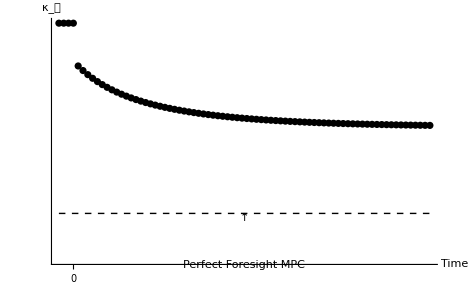

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ctDiscrete/Figures/MPCPathAfterGFall.xxx

```mathematica
MPCPathAfterGFall=Show[MPCPathPlot
,Graphics[{Dashing[{0.01}],Line[{{timePath[[1]],κ},{timePath[[-1]],κ}}]}]
,Graphics[Text["↑",{(timePath[[1]]+timePath[[-1]])/2,κ},{0,1}]]
,Graphics[Text["Perfect Foresight MPC",{(timePath[[1]]+timePath[[-1]])/2,κ(4/5)},{0,1}]]
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","κ_𝓉"}
,PlotRange->All
,AxesOrigin->{-3,0.}];
ExportFigsToDir["MPCPathAfterGFall",FigsDir];
```